# Коцевич Андрей, Б02-920с

## 1 задача

Уравнение Шредингера на радиальную часть волновой функции электрона в атоме водорода (R = u/r):
u''  +   2/ru− (l(l+1))/r^2u=-ϵ u
На больших r наблюдается расходимость. Это связано с отличием от нуля начальной точки.

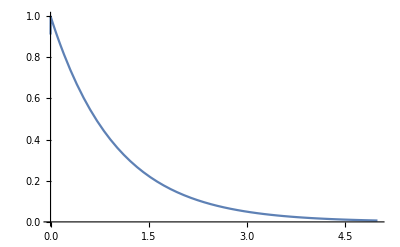

```mathematica
EE =-1;
l=0;
solution = NDSolve[{r^2 uu''[r] + 2r uu[r]-l(l+1)uu[r] == -EE r^2 uu[r], uu'[10^-8]==1,uu[10^-8] == 0}, uu, {r, 10^-8, r1}][[1]];
Plot[uu[r]/r/.solution,{r,10^-8,5}]
```

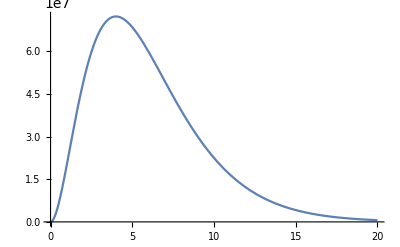

```mathematica
EE =-1/4;
r1 = 20;
l=1;
solution = NDSolve[{r^2 uu''[r] + 2r uu[r]- l(l+1)uu[r] == -EE r^2 uu[r], uu'[10^-8]==1,uu[10^-8] == 0}, uu, {r, 10^-8, r1}][[1]];
Plot[uu[r]/.solution,{r,10^-8,r1}]
```

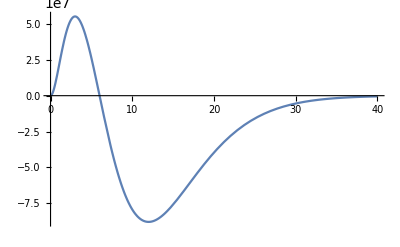

```mathematica
EE =-1/9;
r1=40;
l =1;
solution = NDSolve[{r^2 uu''[r] + 2r uu[r]- l(l+1)uu[r] == -EE r^2 uu[r], uu'[10^-8]==1,uu[10^-8] == 0}, uu, {r, 10^-8, r1}][[1]];
Plot[uu[r]/.solution,{r,10^-8,r1}]
```

## 2 задача

```mathematica
n=2
```

2

```mathematica
q/:
q^(m_):=-q^(m-n)/; (m≥n)
```

## 3 задача*

```mathematica
i /:
i^2:= -1
j /:
j^2:= -1
k /:
k^2:= -1
i j ^:= k
j k ^:= i
k i ^:= j
```